## 134Ce - Petrache study

## Entire structure

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* the YRAST band *)
band8En=Sort[N[#/1000]&@{7550,6776,5864,4761,4006,3207}];
band8Spins=Table[i,{i,10,20,2}];
(* the ONE-PHONON wobbling band *)
band10En=Sort[N[#/1000]&@{6523,5492,4697}];
band10Spins=Table[i,{i,13,17,2}];
(* the YRAST band *)
band9En=Sort[N[#/1000]&@{8583,7581,6597,5724,4907,4183,3719}];
band9Spins=Table[i,{i,10,22,2}];
(* the ONE-PHONON wobbling band *)
band7En=Sort[N[#/1000]&@{5717,4924,4384}];
band7Spins=Table[i,{i,11,15,2}];
```

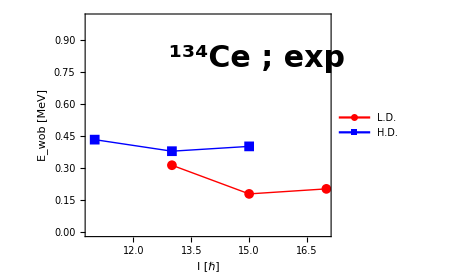

```mathematica
m1minipath="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/Ce-Nucleus/134Ce-joint.pdf";
wobbling1[yrast_,onephonon_,onespins_]:=Table[{onespins[[i]],onephonon[[i]]-1/2(yrast[[i+1]]+yrast[[i+2]])},{i,1,Length[onephonon]}];
wobbling2[yrast_,onephonon_,onespins_]:=Table[{onespins[[i]],onephonon[[i]]-1/2(yrast[[i]]+yrast[[i+1]])},{i,1,Length[onephonon]}];
data1=wobbling1[band8En,band10En,band10Spins];
data2=wobbling2[band9En,band7En,band7Spins];
fig=ListPlot[{data1,data2},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{"L.D.","H.D."},{0.2,0.8}],ImageSize->350,PlotRange->{Full,{0,1}},PlotStyle->{{Red,Thick},{Blue,Thick}},Epilog->{Inset[Style[Row[{Superscript["","134"],"Ce ; exp"}],Bold ,FontFamily->"Arial",30],Scaled[{0.7,0.8}]]}];
Export[m1minipath,fig];
Show[fig]
```